## Approximating the Euler-Mascheroni constant

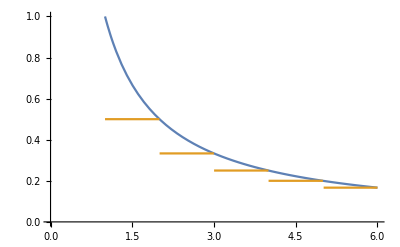

```mathematica
Plot[{1/x,1/Ceiling[x]},{x,1,6},AxesOrigin->{0,0}]
```

```mathematica
Sum[1/2(1/k-1/(k+1)),{k,1,Infinity}]
```

1/2

```mathematica
poly=Simplify[InterpolatingPolynomial[{{k,1/k},{k+1/2,1/(k+1/2)},{k+1,1/(k+1)}},x]]
```

(1+6 k+6 k^2-3 x-6 k x+2 x^2)/(k+3 k^2+2 k^3)

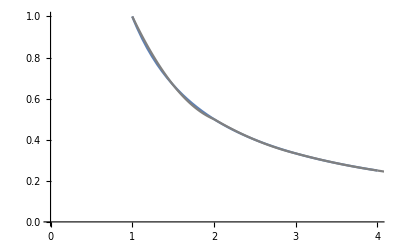

```mathematica
Show[
Plot[1/x,{x,1,4},
AxesOrigin->{0,0}],
Array[Plot[poly/.k->#,{x,#,#+1},PlotStyle->Gray]&,4]
]
```

```mathematica
summand=Simplify[Integrate[poly-1/(k+1),{x,k,k+1}]]
```

(1+6 k)/(6 k+18 k^2+12 k^3)

```mathematica
summand/.k->{1,2,3,4}
```

{7/36,13/180,19/504,5/216}

```mathematica
Sum[summand,{k,1,Infinity}]
```

1/6 (-3+Log[256])

```mathematica
1-N[%]
```

0.575804

```mathematica
EulerGamma//N
```

0.577216

```mathematica
ApproximateEulerGamma[d_Integer?NonNegative]:=
Block[{k,x},
Module[{poly,summand},
With[{points=k+Range[0,d]/d},
poly=InterpolatingPolynomial[Transpose@{points,1/points-1/(k+1)},x];
summand=Integrate[poly,{x,k,k+1}];
1-Sum[summand,{k,1,Infinity}]]]]
```

```mathematica
ApproximateEulerGamma/@{1,2,3,4}//N
```

{0.5,0.575804,0.576561,0.577188}

```mathematica
Abs[%-#]/#&[EulerGamma]
```

{0.133773,0.00244606,0.00113387,0.0000487816}

```mathematica
UnitConvert[%/EulerGamma,"Percent"]
```

{23.1755 %,0.423769 %,0.196438 %,0.00845119 %}